# Geometric optics solutions

## Programming techniques

## Defining rays and optical elements

#### Typed from student sheet

```mathematica
dist[d_]:={{1,d},{0,1}}
MatrixForm[dist[d]] (* only for display *)
```

(1 | d
0 | 1)

#### Answers to questions

-Graphics-

```mathematica
lens[f_]:={{1,0},{-1/f,1}}
mirror[R_]:={{1,0},{-2/R,1}}
plane=IdentityMatrix[2]; (* 2x2 identity matrix *)
```

-Graphics-

```mathematica
x1=40;x1p=-0.2;
{x2,x2p}=dist[300].{x1,x1p};
{x3,x3p}=lens[180].{x2,x2p};
{x4,x4p}=dist[150].{x3,x3p}
```

{-33.3333,-0.0888889}

-Graphics-

```mathematica
Graphics[{{Dotted,Line[{{300,-25},{300,25}}]},
		{Red,InfiniteLine[{{0,0},{1,0}}]},
		{Blue,Line[{{0,x1},{300,x2}}]},
		{Blue,Dashed,HalfLine[{300,x3},{450,x4}]}},PlotRange->{{0,450},{-50,50}}]
```

-Graphics-

-Graphics-

```mathematica
x1=40;x1p=-0.2;
{x2,x2p}=dist[300].{x1,x1p};
{x3,x3p}=lens[180].{x2,x2p};
{x4,x4p}=dist[100].{x3,x3p};
{x5,x5p}=lens[100].{x4,x4p};
{x6,x6p}=dist[50].{x5,x5p}
```

{-18.8889,0.2}

-Graphics-

```mathematica
abcd=dist[50].lens[100].dist[100].lens[180].dist[300];
abcd.{x1,x1p}
```

{-18.8889,0.2}

## Using the predefined functions

#### Typed from student sheet with comments

```mathematica
nb=NotebookOpen["https://www.st-andrews.ac.uk/~ph3080/case/geopt2020b.nb"];
NotebookEvaluate[nb] (* evaluate functions in opened notebook *)
```

```mathematica
Clear[z1,x,xprime,z2,wavelength,z,abcd,diam]
ray={z1->0,x->2,xprime->0.01,z2->Infinity,wavelength->450};
(* 4-f telescope *)
tele={
(* object plane; does not affect rays and a large aperture diameter transmits all rays*)
{z->0,abcd->plane,diam->1000},
(* first lens *)
{z->200,abcd->lens[200],diam->25},
(* second lens *)
{z->800,abcd->lens[400],diam->25},
(* imaging plane *)
{z->1200,abcd->plane,diam->1000}};
```

#### Answers to questions

-Graphics-

```mathematica
ray/.{(wavelength->a_)->(wavelength->620)}
```

{z1→0,x→2,xprime→0.01,z2→∞,wavelength→620}

-Graphics-

```mathematica
rays=Table[ray/.{(x->a_)->(x->x1)},{x1,-5,5,1}];
```

-Graphics-

```mathematica
prays=propagateRays[rays,tele];
```

-Graphics-

```mathematica
Show[showOptics[prays,tele],PlotRange->{{0,1400},{-25,25}},AspectRatio->1]
```

-Graphics-

-Graphics-

```mathematica
dist[400].lens[400].dist[600].lens[200].dist[200]
combineabcd[tele]
```

{{-2,0},{0,-1/2}}

{{-2,0},{0,-1/2}}

## Imaging system

#### Typed from student sheet

```mathematica
(* define single horizontal ray *)
ray={z1->0,x->2,xprime->0,z2->Infinity,wavelength->450};
(* rays from a point source *)
rays=Table[ray/.{(xprime->a_)->(xprime->xp)},{xp,-0.01,0.01,.001}];
```

#### Answers to questions

-Graphics-

```mathematica
prays=propagateRays[rays,tele];
Show[showOptics[prays,tele],PlotRange->{{0,1400},{-25,25}},AspectRatio->1]
```

-Graphics-

## Study:

-Graphics-

```mathematica
ray={z1->0,x->10,xprime->0,z2->Infinity,wavelength->450};
objectEyeRetina={{z->0,abcd->plane,diam->100},{z->400,abcd->lens[17],diam->10},{z->417,abcd->plane,diam->40}};
rays=Table[ray/.{(xprime->a_)->(xprime->xp)},{xp,-0.05,0,0.002}];
prays=propagateRays[rays,objectEyeRetina];

Show[showOptics[prays,objectEyeRetina],PlotRange->{{0,450},{-20,20}},AspectRatio->0.5]
Show[showOptics[prays,objectEyeRetina],PlotRange->{{390,420},{-6,6}},AspectRatio->0.5]
```

-Graphics-

-Graphics-

Initially the focus looks pretty good, with all rays converging on the retina (dotted line). However, if we zoom in we can see that there is a small spread of the rays at the retina, leading to a blurring of the image.

-Graphics-

```mathematica
ClearAll[focusVariance]
focusVariance[fEye_?NumericQ,eyePos_?NumericQ]:=Module[{coneAngle,ray,rays, prays, objectEyeRetina},
ray={z1->0.,x->10.,xprime->0.,z2->Infinity,wavelength->450};
rays=Table[ray/.{(xprime->a_)->(xprime->xp)},{xp,-0.05,0.05,0.002}];
objectEyeRetina={
{z->0,abcd->plane,diam->100},
{z->eyePos,abcd->lens[fEye],diam->10},
{z->eyePos+17,abcd->plane,diam->40}};
prays=propagateRays[rays,objectEyeRetina];
Variance[x/.Select[prays,z2==Infinity/.#&]]//N]
focusVariance[17,400]
focusVariance[17,1000]
focusVariance[17,2000]
```

0.015028

0.00289

0.000578

-Graphics-

Plot the variance graphs with the two requested object positions to get a good starting point from which to minimise the variance.

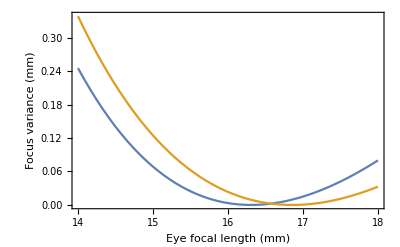

{fEye→16.307}

{fEye→16.8567}

```mathematica
Plot[{focusVariance[fEye,400],focusVariance[fEye,2000]},{fEye,14,18}, Frame->True, FrameLabel->{"Eye focal length (mm)","Focus variance (mm)"}]
focalMin1=FindMinimum[focusVariance[fEye,400],{fEye,16}][[2]]
focalMin2=FindMinimum[focusVariance[fEye,2000],{fEye,16}][[2]]
```

-Graphics-

```mathematica
objectEyeRetina:={
{z->0,abcd->plane,diam->100},
{z->eyePos,abcd->lens[fEye],diam->10},
{z->eyePos+17,abcd->plane,diam->40}};

eyePos=400;fullMatrix1=combineabcd[objectEyeRetina/.focalMin1]

eyePos=2000;
fullMatrix2=combineabcd[objectEyeRetina/.focalMin2]
```

{{-0.0425,-3.10707×10^-6},{-0.0613235,-23.5294}}

{{-0.00850001,-0.0000150278},{-0.0593235,-117.647}}

Notice that the B term in each of these matrices is approximately zero.

{{-0.0425,-3.10707×10^-6},{-0.0613235,-23.5294}}

{{-0.00850001,-0.0000150278},{-0.0593235,-117.647}}

```mathematica
Clear[x1,x1p]
{x2,x2p}={{a,0},{c,d}}.{x1,x1p}
x2/x1
```

{a x1,c x1+d x1p}

a

From a point on the object, any ray with any gradient will converge to a single point in the image - all at height a*x1. So, the ratio of the height at the object to the height at the image is simply the A term in our ABCD matrix, i.e. in any imaging system (B = 0), A is the magnification factor. Note that if this is negative then the image is inverted.

-Graphics-

```mathematica
of=dist[f2].lens[f2].dist[f1+f2].lens[f1].dist[f1]//Simplify;
of//MatrixForm
of[[1,1]]
```

(-f2/f1 | 0
0 | -f1/f2)

-f2/f1

-Graphics-

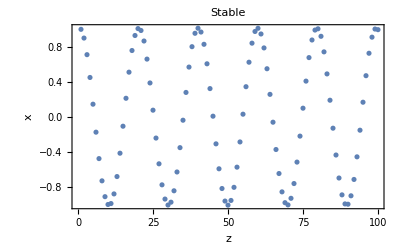

-Graphics-

```mathematica
period=lens[f].dist[d]//Simplify;
r={1,0};
sys1={d->1,f->10.};
rr1=Table[r=period.r/.sys1,{i,100}];
ListPlot[rr1[[All,1]],FrameLabel->{"z","x"},Frame->True, PlotLabel->"Stable"]

r={1,0};
sys2={d->10,f->1.};
rr2=Table[r=period.r/.sys2,{i,100}];
ListPlot[rr2[[All,1]],FrameLabel->{"z","x"},Frame->True, PlotLabel->"Unstable"]
```

```mathematica
(* using our predefined functions *)
period={z->i d,abcd->lens[f],diam->10};
sys1={d->1,f->10.};
sys2={d->10,f->1.};
optics1=Table[period/.sys1,{i,100}];
optics2=Table[period/.sys2,{i,100}];
rays={{z1->0,x->1,xprime->0,z2->∞,wavelength->450}};
prays1=propagateRays[rays,optics1];
prays2=propagateRays[rays,optics2];
Show[showOptics[prays1,optics1], AspectRatio->0.5, PlotLabel->"Stable"]
Show[showOptics[prays2,optics2], AspectRatio->0.5,PlotLabel->"Unstable"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
period=lens[f].dist[d]//Simplify;
r={1,0};
sys1={d->1,f->10.};
ei1=period/.sys1//Eigenvalues
ei2=period/.sys2//Eigenvalues
ei1//Abs
ei2//Abs
```

{0.95+0.31225 ⅈ,0.95-0.31225 ⅈ}

{-7.87298,-0.127017}

{1.,1.}

{7.87298,0.127017}

Eigenvalues with value equal to one, in absolute terms, oscillate as they propagate through the periodic system. Eigenvalues not equal to one indicate that the system diverges.

-Graphics-

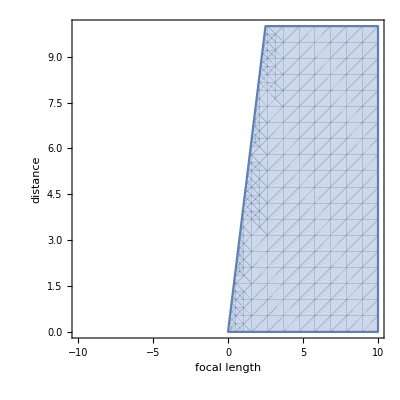

```mathematica
period=lens[f].dist[d];
ei=period//Eigenvalues;
RegionPlot[Abs[ei[[1]]]==1&&Abs[ei[[2]]]==1,{f,-10,10},{d,0,10},FrameLabel->{"focal length","distance"}]
```

-Graphics-

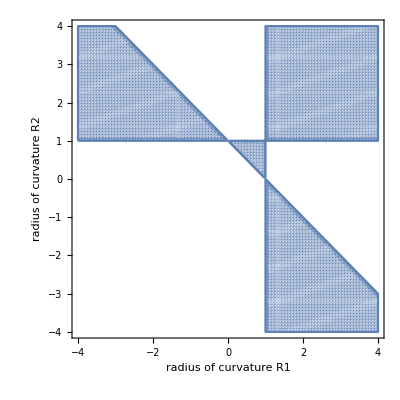

```mathematica
L=1;
period=mirror[R1].dist[L].mirror[R2].dist[L]//Simplify;
ei=period//Eigenvalues;
RegionPlot[Abs[ei[[1]]]==1&&Abs[ei[[2]]]==1,{R1,-4,4},{R2,-4,4},PlotPoints->100,FrameLabel->{"radius of curvature R1","radius of curvature R2"}]
```

## Advanced problem

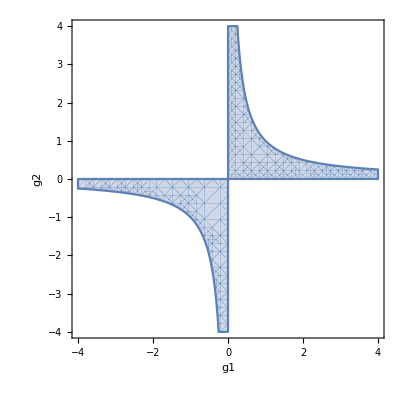

```mathematica
L=1;
period=mirror[L/(1-g1)].dist[L].mirror[L/(1-g2)].dist[L]//Simplify;
ei=period//Eigenvalues;
RegionPlot[Abs[ei[[1]]]==1&&Abs[ei[[2]]]==1,{g1,-4,4},{g2,-4,4},FrameLabel->{"g1","g2"}]
```